```mathematica
k[n_] := If[Mod[n+1, 2] == 0, Subscript[k, e], Subscript[k, o]]
```

```mathematica
q [N_] := Sin[π *Range[0,N+1]/(N+1)]
```

```mathematica
dof = 14
```

14

```mathematica
Q = q[dof]
```

{0,Sin[π/15],Sin[(2 π)/15],√(5/8-(√5)/8),Cos[(7 π)/30],(√3)/2,√(5/8+(√5)/8),Cos[π/30],Cos[π/30],√(5/8+(√5)/8),(√3)/2,Cos[(7 π)/30],√(5/8-(√5)/8),Sin[(2 π)/15],Sin[π/15],0}

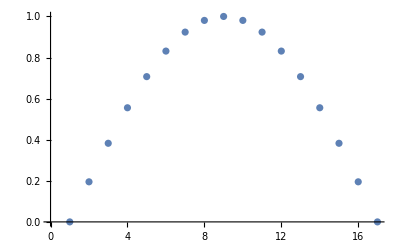

```mathematica
ListPlot[Q]
```

```mathematica
dq = Q[[2;;-1]] - Q[[1;;-2]]
```

{Sin[π/15],-Sin[π/15]+Sin[(2 π)/15],√(5/8-(√5)/8)-Sin[(2 π)/15],-√(5/8-(√5)/8)+Cos[(7 π)/30],(√3)/2-Cos[(7 π)/30],-(√3)/2+√(5/8+(√5)/8),-√(5/8+(√5)/8)+Cos[π/30],0,√(5/8+(√5)/8)-Cos[π/30],(√3)/2-√(5/8+(√5)/8),-(√3)/2+Cos[(7 π)/30],√(5/8-(√5)/8)-Cos[(7 π)/30],-√(5/8-(√5)/8)+Sin[(2 π)/15],Sin[π/15]-Sin[(2 π)/15],-Sin[π/15]}

```mathematica
V = Sum[k[n]*((dq[[n]])^2/2 + α/3 (dq[[n]])^3),{n,dof+1}]/.α->0.25
```

0.0929947 k_e+0.0708982 k_o

```mathematica
E0  = V/.Subscript[k, e] ->1/.Subscript[k, o]->1
```

0.163893

```mathematica
NSolve[V == E0 && Subscript[k, e]/Subscript[k, o] == 0.5, {Subscript[k, e], Subscript[k, o]}]
```

{{k_e→0.698037,k_o→1.39607}}

```mathematica
NSolve[V == E0 && Subscript[k, e]/Subscript[k, o] == 2, {Subscript[k, e], Subscript[k, o]}]
```

{{k_e→1.27599,k_o→0.637995}}